# Surprises in a classic boundary-layer problem

## Companion notebook: perturbation theory and matching calculations

Author: Leo C. Stein (leo.stein@gmail.com)
Date: 2021 July

This notebook is a companion to the article of the same name [arXiv:2107.11624].
Please contact the authors for questions about use, attribution, and distribution.

### 0. Utility functions

```mathematica
LminusR[a_==b_]:=a-b
```

```mathematica
Off[RuleDelayed::rhs];
RuleToSetDelayed[rule:(s_Symbol->Verbatim[Function][{x_},body_])]:=Module[{},
SetDelayed[s[x_],body];
Print["Rule ",Shallow[rule]," has been set for symbol ",s];]
On[RuleDelayed::rhs];
RuleToSetDelayed[{a_->b_}]:=RuleToSetDelayed[a->b]
```

This is for silly plotting stuff

```mathematica
VertLine[x_]:=InfiniteLine[{{x,0},{x,1}}]
```

### 1. Introduction

We start with the ODE and the boundary conditions

```mathematica
ODEEq={ϵ y''[x]==y[x]y'[x]-y[x]};
BCEqs={y[0]==1,y[1]==-1};
```

### 5. Perturbation theory

#### 5.1 Outer solutions

Develop the ODEs for a perturbation expansion in the “outer” (slow) regions.  Use Mathematica’s builtin Series[] command (which is annoying on equations, so apply it to LHS-RHS

```mathematica
LminusR@ODEEq[[1]]/.{y->Function[x,y0[x]+ϵ y1[x]]}
OuterODE01Terms=Series[%,{ϵ,0,1}]
OuterODE0=SeriesCoefficient[OuterODE01Terms,{ϵ,0,0}]==0
```

y0[x]+ϵ y1[x]-(y0[x]+ϵ y1[x]) (y0'[x]+ϵ y1'[x])+ϵ (y0''[x]+ϵ y1''[x])

(y0[x]-y0[x] y0'[x])+(y1[x]-y1[x] y0'[x]-y0[x] y1'[x]+y0''[x]) ϵ+O[ϵ]^2

y0[x]-y0[x] y0'[x]==0

Here are the general solutions for y0[x] in the outer region:

```mathematica
y0Sols=DSolve[OuterODE0,y0,x]
```

{{y0→Function[{x},0]},{y0→Function[{x},x+C[1]]}}

For either of these cases, notice that all higher orders in perturbation theory y_n(x) will vanish. First the 0 solution for y_0:

```mathematica
SeriesCoefficient[OuterODE01Terms,{ϵ,0,1}]==0
%/.y0Sols[[1]]
```

y1[x]-y1[x] y0'[x]-y0[x] y1'[x]+y0''[x]==0

y1[x]==0

Next, the linear solution for y_0, along with a boundary condition that y_1(x)=0 at a boundary in the domain (since the 0th order will already satisfy the BC):

```mathematica
SeriesCoefficient[OuterODE01Terms,{ϵ,0,1}]==0
%/.y0Sols[[2]]
DSolve[%,y1,x]
```

y1[x]-y1[x] y0'[x]-y0[x] y1'[x]+y0''[x]==0

-(x+C[1]) y1'[x]==0

{{y1→Function[{x},C[2]]}}

The constant above must be 0.

Ok, let’s impose the left/right BCs for y0 and save those solutions!

```mathematica
y0LSol=First@DSolve[{OuterODE0,BCEqs[[1]]/.y->y0}/.y0->y0L,y0L,x]
RuleToSetDelayed[y0LSol]
y0RSol=First@DSolve[{OuterODE0,BCEqs[[2]]/.y->y0}/.y0->y0R,y0R,x]
RuleToSetDelayed[y0RSol]
```

DSolve::bvnul: For some branches of the general solution, the given boundary conditions lead to an empty solution.

{y0L→Function[{x},1+x]}

Rule y0L→Function[{«1»},Plus[«2»]] has been set for symbol y0L

DSolve::bvnul: For some branches of the general solution, the given boundary conditions lead to an empty solution.

{y0R→Function[{x},-2+x]}

Rule y0R→Function[{«1»},Plus[«2»]] has been set for symbol y0R

#### 5.2 Inner equation

Find the distinguished limit. The only dominant balance that works is making the ϵ/δ^2 term match the 1/δ term.

```mathematica
ODEEq[[1]]/.y->Function[{x},Y[(x-x0)/δ]]/.{x->x0+δ X}
%/.δ->ϵ
InnerODEEq={(ϵ #)&/@%//Expand}
```

(ϵ Y''[X])/δ^2==-Y[X]+(Y[X] Y'[X])/δ

Y''[X]/ϵ==-Y[X]+(Y[X] Y'[X])/ϵ

{Y''[X]==-ϵ Y[X]+Y[X] Y'[X]}

#### 5.3 Leading-order inner solution

Again, start to develop the series expansion

```mathematica
LminusR@InnerODEEq[[1]]/.{Y->Function[x,Y0[x]+ϵ Y1[x]]}
InnerODE01Terms=Series[%,{ϵ,0,1}]
InnerODE0=SeriesCoefficient[InnerODE01Terms,{ϵ,0,0}]==0
```

ϵ (Y0[X]+ϵ Y1[X])-(Y0[X]+ϵ Y1[X]) (Y0'[X]+ϵ Y1'[X])+Y0''[X]+ϵ Y1''[X]

(-Y0[X] Y0'[X]+Y0''[X])+(Y0[X]-Y1[X] Y0'[X]-Y0[X] Y1'[X]+Y1''[X]) ϵ+O[ϵ]^2

-Y0[X] Y0'[X]+Y0''[X]==0

Solve the leading-order equation. Mathematica took a turn in the complex plane; turn back!

```mathematica
Y0Sol=First@DSolve[InnerODE0,Y0,X]
```

{Y0→Function[{X},√2 √C[1] Tan[1/2 (√2 X √C[1]+√2 √C[1] C[2])]]}

Just relabel coefficients to get to the solution we want:

```mathematica
Y0[X]/.Y0Sol/.{C[1]->-b^2/2,C[2]->(-2c)/b}//ComplexExpand
Y0SolValue=Simplify[%,Assumptions->{b>0}]
```

-(√(b^2) Sinh[2 (-(√(b^2) c)/b+(√(b^2) X)/2)])/(1+Cosh[2 (-(√(b^2) c)/b+(√(b^2) X)/2)])

b Tanh[c-(b X)/2]

#### 5.4 Zeroth-order matching for the symmetric solution M

When our layer is at x=1/2, we have the symmetric solution. We need Y[X=0]=0. Choose a real solution.

```mathematica
0==Y0SolValue/.X->0
First@Solve[%,c]
%/.C[1]->0
Y0MSolValue1=Y0SolValue/.%
```

0==b Tanh[c]

{c→ConditionalExpression[ⅈ π C[1], C[1]∈ℤ]}

{c→0}

-b Tanh[(b X)/2]

```mathematica
Y0MSolValue1=Y0SolValue/.c->0
```

-b Tanh[(b X)/2]

We need to satisfy these conditions. They are both satisfied by the same value of b, phew!

```mathematica
y0L[1/2]==Limit[Y0MSolValue1,X->-∞]
y0R[1/2]==Limit[Y0MSolValue1,X->+∞]
Y0MSolValue2=Y0MSolValue1/.First@Solve[%,b]
```

ConditionalExpression[3/2==b, b>0]

ConditionalExpression[-3/2==-b, b>0]

-3/2 Tanh[(3 X)/4]

Save this function

```mathematica
Y0MRule={Y0M->Function[{X},Evaluate@Y0MSolValue2]}
RuleToSetDelayed[Y0MRule]
```

{Y0M→Function[{X},-3/2 Tanh[(3 X)/4]]}

Rule Y0M→Function[{«1»},Times[«2»]] has been set for symbol Y0M

Construct the composite solution:

```mathematica
y0L[x]+Y0M[(x-1/2)/ϵ]-y0L[1/2]
yc0MRule={yc0M->Function[{x},Evaluate@%]}
RuleToSetDelayed[yc0MRule]
```

-1/2+x-3/2 Tanh[(3 (-1/2+x))/(4 ϵ)]

{yc0M→Function[{x},-1/2+x-3/2 Tanh[(3 (-1/2+x))/(4 ϵ)]]}

Rule yc0M→Function[{«1»},Plus[«3»]] has been set for symbol yc0M

#### 5.5 Zeroth-order matching for the asymmetric solutions B0 and B1

When our layer is at x=0, then leaving the layer X→∞ means we need to match to y0R[0]

```mathematica
y0R[0]==Limit[Y0SolValue,X->∞,Assumptions->{b<0}]
Y0B0SolValue1=Y0SolValue/.First@Solve[%,b]
```

-2==b

-2 Tanh[c+X]

Now satisfy the boundary condition Y(0)=1. Choose a real solution.

```mathematica
1==Y0B0SolValue1/.X->0
First@Solve[%,c]
%/.C[1]->0
Y0B0SolValue2=Y0B0SolValue1/.%
```

1==-2 Tanh[c]

{c→ConditionalExpression[-ArcTanh[1/2]+ⅈ π C[1], C[1]∈ℤ]}

{c→-ArcTanh[1/2]}

-2 Tanh[X-ArcTanh[1/2]]

Save this function

```mathematica
Y0B0Rule={Y0B0->Function[{X},Evaluate@Y0B0SolValue2]}
RuleToSetDelayed[Y0B0Rule]
```

{Y0B0→Function[{X},-2 Tanh[X-ArcTanh[1/2]]]}

Rule Y0B0→Function[{«1»},Times[«2»]] has been set for symbol Y0B0

Construct the composite solution:

```mathematica
y0R[x]+Y0B0[x/ϵ]-y0R[0]
yc0B0Rule={yc0B0->Function[{x},Evaluate@%]}
RuleToSetDelayed[yc0B0Rule]
```

x-2 Tanh[x/ϵ-ArcTanh[1/2]]

{yc0B0→Function[{x},x-2 Tanh[x/ϵ-ArcTanh[1/2]]]}

Rule yc0B0→Function[{«1»},Plus[«2»]] has been set for symbol yc0B0

Not much to do for the B1 solution — just use symmetry. Here, the layer is still at X=0, but going in the opposite direction because of x→1-x

```mathematica
Y0B0SolValue2
Y0B1SolValue=-%/.{X->-X}
```

-2 Tanh[X-ArcTanh[1/2]]

-2 Tanh[X+ArcTanh[1/2]]

```mathematica
Y0B1Rule={Y0B1->Function[{X},Evaluate@Y0B1SolValue]}
RuleToSetDelayed[Y0B1Rule]
```

{Y0B1→Function[{X},-2 Tanh[X+ArcTanh[1/2]]]}

Rule Y0B1→Function[{«1»},Times[«2»]] has been set for symbol Y0B1

Construct the composite solution:

```mathematica
y0L[x]+Y0B1[(x-1)/ϵ]-y0L[1]
yc0B1Rule={yc0B1->Function[{x},Evaluate@%]}
RuleToSetDelayed[yc0B1Rule]
```

-1+x-2 Tanh[(-1+x)/ϵ+ArcTanh[1/2]]

{yc0B1→Function[{x},-1+x-2 Tanh[(-1+x)/ϵ+ArcTanh[1/2]]]}

Rule yc0B1→Function[{«1»},Plus[«3»]] has been set for symbol yc0B1

#### 5.6 / Appendix A, First-order matching for the symmetric solution M

Now we will break a sweat! Push the inner solution to order ϵ^1. First, get the general ODE for Y1:

```mathematica
InnerODE1=SeriesCoefficient[InnerODE01Terms,{ϵ,0,1}]==0
```

Y0[X]-Y1[X] Y0'[X]-Y0[X] Y1'[X]+Y1''[X]==0

Now specialize to the case of Y^M:

```mathematica
InnerODEY1M=InnerODE1/.{Y0->Y0M,Y1->Y1M}
```

-3/2 Tanh[(3 X)/4]+9/8 Sech[(3 X)/4]^2 Y1M[X]+3/2 Tanh[(3 X)/4] Y1M'[X]+Y1M''[X]==0

And Mma can solve it!

```mathematica
Y1MSol=First@DSolve[InnerODEY1M,Y1M,X]
```

{Y1M→Function[{X},C[2] Sech[(3 X)/4]^2+1/24 Sech[(3 X)/4]^2 (3 X (4-3 X+4 C[1]-8 Log[1+ⅇ^(-3 X/2)]+8 Log[Cosh[(3 X)/4]])+16 PolyLog[2,-ⅇ^(-3 X/2)]+8 (-1+C[1]+2 Log[Cosh[(3 X)/4]]) Sinh[(3 X)/2])]}

```mathematica
FullSimplify[Y1M[X]/.Y1MSol,Assumptions->{X∈Reals}]
```

1/24 Sech[(3 X)/4]^2 (24 C[2]+3 X (4+3 X+4 C[1]-4 Log[4])+16 PolyLog[2,-ⅇ^(-3 X/2)]+8 (-1+C[1]+2 Log[Cosh[(3 X)/4]]) Sinh[(3 X)/2])

Now our job is to figure out the free coefficients. First, use symmetry.

```mathematica
0==Y1M[0]/.Y1MSol
First@Solve[%]
Y1MSol2=Y1MSol/.%
```

0==-π^2/18+C[2]

{C[2]→π^2/18}

{Y1M→Function[{X},1/18 π^2 Sech[(3 X)/4]^2+1/24 Sech[(3 X)/4]^2 (3 X (4-3 X+4 C[1]-8 Log[1+ⅇ^(-3 X/2)]+8 Log[Cosh[(3 X)/4]])+16 PolyLog[2,-ⅇ^(-3 X/2)]+8 (-1+C[1]+2 Log[Cosh[(3 X)/4]]) Sinh[(3 X)/2])]}

Now we have the harder job of performing the asymptotic expansion. Unfortunately, Mma’s Series[] and Asymptotic[] aren’t happy with these functions. We will provide a lot of manual guidance, be careful! Important steps here: 
(i) After massaging a bit, we have Log[1+Exp[-3X/2]], when taking X→∞, expand Log[1+z] for z<<1.
(ii) At that point, the only exponentials are negative when taking X→∞, drop them as they are TST.
(iii) Match the asymptotic behavior X+const should be X+O(ϵ), so that constant should vanish.

```mathematica
Y1M[X]/.Y1MSol2
%/.{expr:(Sech|Cosh|Sinh|PolyLog)[__]:>Asymptotic[expr,X->∞]}
%/.{expr:Log[_]:>FullSimplify[expr,Assumptions->{X∈Reals}]}
%/.{Log[1+a_]:>a}//Simplify
Series[%,{X,∞,1}]
%/.Exp[_]->0
First@Solve[X==Normal@%,C[1]]
Y1MSol3=Y1MSol2/.%
```

1/18 π^2 Sech[(3 X)/4]^2+1/24 Sech[(3 X)/4]^2 (3 X (4-3 X+4 C[1]-8 Log[1+ⅇ^(-3 X/2)]+8 Log[Cosh[(3 X)/4]])+16 PolyLog[2,-ⅇ^(-3 X/2)]+8 (-1+C[1]+2 Log[Cosh[(3 X)/4]]) Sinh[(3 X)/2])

2/9 ⅇ^(-3 X/2) π^2+1/6 ⅇ^(-3 X/2) (-16 ⅇ^(-3 X/2)+4 ⅇ^(3 X/2) (-1+C[1]+2 Log[1/2 ⅇ^(3 X/4)])+3 X (4-3 X+4 C[1]+8 Log[1/2 ⅇ^(3 X/4)]-8 Log[1+ⅇ^(-3 X/2)]))

2/9 ⅇ^(-3 X/2) π^2+1/6 ⅇ^(-3 X/2) (-16 ⅇ^(-3 X/2)+4 ⅇ^(3 X/2) (-1+C[1]+2 ((3 X)/4-Log[2]))+3 X (4-3 X+4 C[1]+8 ((3 X)/4-Log[2])-8 Log[1+ⅇ^(-3 X/2)]))

1/18 (-24 ⅇ^(-3 X) (2+3 X)+ⅇ^(-3 X/2) (4 π^2+9 X (4+3 X+4 C[1]-8 Log[2]))+6 (-2+3 X+2 C[1]-4 Log[2]))

ⅇ^(-3 X+O[1/X]^2) (-4 X-8/3+O[1/X]^2)+(X+2/3 (-1+C[1]-2 Log[2])+O[1/X]^2)+ⅇ^(-(3 X)/2+O[1/X]^2) ((3 X^2)/2+2 (1+C[1]-2 Log[2]) X+(2 π^2)/9+O[1/X]^2)

X+2/3 (-1+C[1]-2 Log[2])+O[1/X]^2

{C[1]→1+2 Log[2]}

{Y1M→Function[{X},1/18 π^2 Sech[(3 X)/4]^2+1/24 Sech[(3 X)/4]^2 (3 X (4-3 X+4 (1+2 Log[2])-8 Log[1+ⅇ^(-3 X/2)]+8 Log[Cosh[(3 X)/4]])+16 PolyLog[2,-ⅇ^(-3 X/2)]+8 (-1+(1+2 Log[2])+2 Log[Cosh[(3 X)/4]]) Sinh[(3 X)/2])]}

Save this function

```mathematica
RuleToSetDelayed[Y1MSol3]
```

Rule Y1M→Function[{«1»},Plus[«2»]] has been set for symbol Y1M

```mathematica
FullSimplify[Y1M[X],Assumptions->{X∈Reals}]
```

1/72 Sech[(3 X)/4]^2 (4 π^2+9 X (8+3 X)+48 PolyLog[2,-ⅇ^(-3 X/2)]+48 Log[2 Cosh[(3 X)/4]] Sinh[(3 X)/2])

Now construct the composite solution. Funny enough, this time y_match is itself y0L or y0R, depending on which side you think we matched on.

```mathematica
y0L[x]+Y0M[(x-1/2)/ϵ]+ϵ Y1M[(x-1/2)/ϵ]-y0L[x]//Simplify
yc1MRule={yc1M->Function[{x},Evaluate@%]}
RuleToSetDelayed[yc1MRule]
```

1/72 (4 π^2 ϵ Sech[(3 (-1+2 x))/(8 ϵ)]^2+3 ϵ Sech[(3 (-1+2 x))/(8 ϵ)]^2 ((3 (-1/2+x) (8+3/(2 ϵ)-(3 x)/ϵ+Log[256]-8 Log[1+ⅇ^((3-6 x)/(4 ϵ))]+8 Log[Cosh[(3 (-1+2 x))/(8 ϵ)]]))/ϵ+16 PolyLog[2,-ⅇ^((3-6 x)/(4 ϵ))]+16 (Log[2]+Log[Cosh[(3 (-1+2 x))/(8 ϵ)]]) Sinh[(3 (-1+2 x))/(4 ϵ)])-108 Tanh[(3 (-1+2 x))/(8 ϵ)])

{yc1M→Function[{x},1/72 (4 π^2 ϵ Sech[(3 (-1+2 x))/(8 ϵ)]^2+3 ϵ Sech[(3 (-1+2 x))/(8 ϵ)]^2 ((3 (-1/2+x) (8+3/(2 ϵ)-(3 x)/ϵ+Log[256]-8 Log[1+ⅇ^((3-6 x)/(4 ϵ))]+8 Log[Cosh[(3 (-1+2 x))/(8 ϵ)]]))/ϵ+16 PolyLog[2,-ⅇ^((3-6 x)/(4 ϵ))]+16 (Log[2]+Log[Cosh[(3 (-1+2 x))/(8 ϵ)]]) Sinh[(3 (-1+2 x))/(4 ϵ)])-108 Tanh[(3 (-1+2 x))/(8 ϵ)])]}

Rule yc1M→Function[{«1»},Times[«2»]] has been set for symbol yc1M

#### 5.6 / Appendix A, First-order matching for the asymmetric solutions B0 and B1

This is similar to the M case above.

```mathematica
InnerODEY1B0=InnerODE1/.{Y0->Y0B0,Y1->Y1B0}
```

-2 Tanh[X-ArcTanh[1/2]]+2 Sech[X-ArcTanh[1/2]]^2 Y1B0[X]+2 Tanh[X-ArcTanh[1/2]] Y1B0'[X]+Y1B0''[X]==0

```mathematica
Y1B0Sol=First@DSolve[InnerODEY1B0,Y1B0,X]
```

{Y1B0→Function[{X},C[2] Sech[X-ArcTanh[1/2]]^2+1/4 Sech[X-ArcTanh[1/2]]^2 (-2 (X-ArcTanh[1/2]) (-1+X-ArcTanh[1/2]-C[1]+2 Log[1+ⅇ^(-2 X+2 ArcTanh[1/2])]-2 Log[Cosh[X-ArcTanh[1/2]]])+2 PolyLog[2,-ⅇ^(-2 X+2 ArcTanh[1/2])]+(-1+C[1]+2 Log[Cosh[X-ArcTanh[1/2]]]) Sinh[2 X-2 ArcTanh[1/2]])]}

```mathematica
1/4 Sech[X̄]^2 (4 C[2]+2 X̄ (1+C[1]-2Log[2]+X̄)+2 PolyLog[2,-ⅇ^(-2 X̄)]+(-1+C[1]+2 Log[Cosh[X̄]]) Sinh[2 X̄])
FullSimplify[(Y1B0[X]/.Y1B0Sol/.{X->X̄+ArcTanh[1/2]})==%,Assumptions->{X̄∈Reals}]
```

1/4 Sech[X̄]^2 (4 C[2]+2 X̄ (1+C[1]-2 Log[2]+X̄)+2 PolyLog[2,-ⅇ^(-2 X̄)]+(-1+C[1]+2 Log[Cosh[X̄]]) Sinh[2 X̄])

True

Apply Asymptotic[] where it works; get to the point where the only log is Log[1+3Exp[-2X]], and expand Log[1+z] for z<<1; then when all exponentials have a negative number times X as an argument, drop those exponentials. Finally match the asymptotic from to X+O(ϵ) to fix the constant.

```mathematica
Y1B0[X]/.Y1B0Sol;
%/.{expr:(Sech|Cosh|Sinh|PolyLog)[__]:>Asymptotic[expr,X->∞]}
%/.{expr:Log[_]:>FullSimplify[expr,Assumptions->{X∈Reals}]}
%/.{Log[1+a_]:>a}//Simplify
Series[%,{X,∞,1}]
%/.Exp[arg_]/;(!FreeQ[arg,X])->0
First@Solve[X==Normal@%,C[1]]
Y1B0Sol1=Y1B0Sol/.%
```

4 ⅇ^(-2 X+2 ArcTanh[1/2]) C[2]+ⅇ^(-2 X+2 ArcTanh[1/2]) (-2 ⅇ^(-2 X+2 ArcTanh[1/2])+1/2 ⅇ^(2 X-2 ArcTanh[1/2]) (-1+C[1]+2 Log[1/2 ⅇ^(X-ArcTanh[1/2])])-2 (X-ArcTanh[1/2]) (-1+X-ArcTanh[1/2]-C[1]-2 Log[1/2 ⅇ^(X-ArcTanh[1/2])]+2 Log[1+ⅇ^(-2 X+2 ArcTanh[1/2])]))

4 ⅇ^(-2 X+2 ArcTanh[1/2]) C[2]+ⅇ^(-2 X+2 ArcTanh[1/2]) (-2 ⅇ^(-2 X+2 ArcTanh[1/2])+1/2 ⅇ^(2 X-2 ArcTanh[1/2]) (-1+C[1]+2 (X-Log[12]/2))-2 (X-ArcTanh[1/2]) (-1+X-ArcTanh[1/2]-C[1]-2 (X-Log[12]/2)+2 Log[1+3 ⅇ^(-2 X)]))

1/2 ⅇ^(-4 X) (-4 ⅇ^(4 ArcTanh[1/2])+24 ⅇ^(2 ArcTanh[1/2]) (-X+ArcTanh[1/2])+ⅇ^(4 X) (-1+2 X+C[1]-Log[12])+4 ⅇ^(2 (X+ArcTanh[1/2])) (X^2-ArcTanh[1/2]-ArcTanh[1/2]^2-ArcTanh[1/2] C[1]+2 C[2]+X (1+C[1]-Log[12])+ArcTanh[1/2] Log[12]))

(X+1/2 (-1+C[1]-Log[12])+O[1/X]^2)+ⅇ^(-4 X+O[1/X]^3) (-12 ⅇ^(2 ArcTanh[1/2]) X-2 (ⅇ^(2 ArcTanh[1/2]) (ⅇ^(2 ArcTanh[1/2])-6 ArcTanh[1/2]))+O[1/X]^2)+ⅇ^(-2 X+2 ArcTanh[1/2]+O[1/X]^3) (2 X^2+2 (1+C[1]-Log[12]) X-2 (ArcTanh[1/2]+ArcTanh[1/2]^2+ArcTanh[1/2] C[1]-2 C[2]-ArcTanh[1/2] Log[12])+O[1/X]^2)

X+1/2 (-1+C[1]-Log[12])+O[1/X]^2

{C[1]→1+Log[12]}

{Y1B0→Function[{X},C[2] Sech[X-ArcTanh[1/2]]^2+1/4 Sech[X-ArcTanh[1/2]]^2 (-2 (X-ArcTanh[1/2]) (-1+X-ArcTanh[1/2]-(1+Log[12])+2 Log[1+ⅇ^(-2 X+2 ArcTanh[1/2])]-2 Log[Cosh[X-ArcTanh[1/2]]])+2 PolyLog[2,-ⅇ^(-2 X+2 ArcTanh[1/2])]+(-1+(1+Log[12])+2 Log[Cosh[X-ArcTanh[1/2]]]) Sinh[2 X-2 ArcTanh[1/2]])]}

Fix the other constant by satisfying the boundary condition at x=0. Since Y_0 already satisfies Y_0(0)=1, we want Y_1(0)=0.

```mathematica
Y1B0[0]/.Y1B0Sol1//FullSimplify
Y1B0C2sol=First@Solve[0==%,C[2]]
N[Y1B0C2sol]
Y1B0Sol2=Y1B0Sol1/.Y1B0C2sol
```

1/32 (24 C[2]-3 Log[3]^2-4 Log[6912]+12 PolyLog[2,-3])

{C[2]→1/24 (3 Log[3]^2+4 Log[6912]-12 PolyLog[2,-3])}

{C[2]→2.59406}

{Y1B0→Function[{X},1/24 (3 Log[3]^2+4 Log[6912]-12 PolyLog[2,-3]) Sech[X-ArcTanh[1/2]]^2+1/4 Sech[X-ArcTanh[1/2]]^2 (-2 (X-ArcTanh[1/2]) (-1+X-ArcTanh[1/2]-(1+Log[12])+2 Log[1+ⅇ^(-2 X+2 ArcTanh[1/2])]-2 Log[Cosh[X-ArcTanh[1/2]]])+2 PolyLog[2,-ⅇ^(-2 X+2 ArcTanh[1/2])]+(-1+(1+Log[12])+2 Log[Cosh[X-ArcTanh[1/2]]]) Sinh[2 X-2 ArcTanh[1/2]])]}

Save this function

```mathematica
RuleToSetDelayed[Y1B0Sol2]
```

Rule Y1B0→Function[{«1»},Plus[«2»]] has been set for symbol Y1B0

```mathematica
FullSimplify[Y1B0[X],Assumptions->{X∈Reals}]
```

1/12 Sech[X-ArcCoth[2]]^2 (6 X (2+X)+Log[65536]-6 PolyLog[2,-3]+6 PolyLog[2,-3 ⅇ^(-2 X)]+3 Log[12 Cosh[X-ArcCoth[2]]^2] Sinh[2 X-2 ArcCoth[2]])

Construct the composite solution. Funny enough, this time y_match is itself y0R.

```mathematica
y0R[x]+Y0B0[x/ϵ]+ϵ Y1B0[x/ϵ]-y0R[x]//Simplify
yc1B0Rule={yc1B0->Function[{x},Evaluate@%]};
RuleToSetDelayed[yc1B0Rule]
```

1/24 ϵ (3 Log[3]^2+4 (Log[6912]-3 PolyLog[2,-3])) Sech[x/ϵ-ArcTanh[1/2]]^2+1/4 ϵ Sech[x/ϵ-ArcTanh[1/2]]^2 (-(2 (-x+ϵ ArcTanh[1/2]) (-x+2 ϵ+ϵ ArcTanh[1/2]+ϵ Log[12]-2 ϵ Log[1+ⅇ^(-(2 x)/ϵ+2 ArcTanh[1/2])]+2 ϵ Log[Cosh[x/ϵ-ArcTanh[1/2]]]))/ϵ^2+2 PolyLog[2,-ⅇ^(-(2 x)/ϵ+2 ArcTanh[1/2])]+(Log[12]+2 Log[Cosh[x/ϵ-ArcTanh[1/2]]]) Sinh[(2 x)/ϵ-2 ArcTanh[1/2]])-2 Tanh[x/ϵ-ArcTanh[1/2]]

Rule yc1B0→Function[{«1»},Plus[«3»]] has been set for symbol yc1B0

Not much to do for the B1 solution — just use symmetry.

```mathematica
yc1B1[x_]:=-yc1B0[1-x]
```

### 6. Solving for the initial slope

#### 6.1 Initial slope for B0

At zeroth order — incomplete!

```mathematica
yc0B0[0]
yc0B0'[0]
```

1

1-3/(2 ϵ)

At first order — good enough

```mathematica
yc1B0[0]//FullSimplify
yc1B0'[0]//FullSimplify
```

1

1-3/(2 ϵ)+Log[16]

#### 6.2. Initial slope: The tempting but wrong way

We need some extra tooling, because Asymptotic[] and Series[] won’t do the expansions we seek. First, how to collect controlling factors in sums:

```mathematica
ExpPowerOverEps[a_. ⅇ^(b_/ϵ)]:=b
ExpPowerOverEps[a_]:=0
```

```mathematica
ControllingFactor[sum_Plus]:=TakeLargestBy[List@@sum,ExpPowerOverEps,1][[1]]
```

```mathematica
CollectControllingFactor[sum_Plus]:=With[{cf=ControllingFactor[sum]},
cf Expand[sum/cf]]
CollectControllingFactors[expr_]:=expr/.{sum_Plus:>CollectControllingFactor[sum]}
```

Binomial expansion of 1/(1+x)^p=1-p x+O(x^2), which we use to get rid of denominators up to TST

```mathematica
ExpandTSTDenoms[expr_]:=expr//.{(1+(a_:1) ⅇ^(b_/ϵ))^p_/;((p<0)&&(b<0)):>1+p a ⅇ^(b/ϵ)}
```

If we want to drop TST terms in a sum — only use this if you’ve collected the controlling factor out in front!
I am only implementing a very restricted form, to make sure we don’t mess up

```mathematica
AllExpsNegative[expr_]:=With[{pows=Cases[expr,Exp[b_/ϵ]:>b,All]},
And@@(Negative/@pows)]
```

```mathematica
DropTSTs[1+a_]/;AllExpsNegative[a]:=1+a/.Exp[_]->0
```

Ok, let’s compute 1-y_(c,0)^M:

```mathematica
1-yc0M[0]
%//TrigToExp//Together
CollectControllingFactors@%
%//ExpandTSTDenoms
MapAt[DropTSTs,%,3]
```

3/2-3/2 Tanh[3/(8 ϵ)]

3/(1+ⅇ^(3/4/ϵ))

(3 ⅇ^(-3/4/ϵ))/(1+ⅇ^(-3/4/ϵ))

3 ⅇ^(-3/4/ϵ) (1-ⅇ^(-3/4/ϵ))

3 ⅇ^(-3/4/ϵ)

That is, we found y_(c,0)^M(0)~1-3Exp[-3/(4ϵ)]+TST. Now the derivative:

```mathematica
1-yc0M'[0]
%//TrigToExp//Together
%//CollectControllingFactors
%//ExpandTSTDenoms
MapAt[DropTSTs,%,3]
```

(9 Sech[3/(8 ϵ)]^2)/(8 ϵ)

(9 ⅇ^(3/4/ϵ))/(2 (1+ⅇ^(3/4/ϵ))^2 ϵ)

(9 ⅇ^(-3/4/ϵ))/(2 (1+ⅇ^(-3/4/ϵ))^2 ϵ)

(9 ⅇ^(-3/4/ϵ) (1-2 ⅇ^(-3/4/ϵ)))/(2 ϵ)

(9 ⅇ^(-3/4/ϵ))/(2 ϵ)

That is, we found y_(c,0)^M'(0)~1-9/(2ϵ)Exp[-3/(4ϵ)]+TST.

Now on to y_(c,1)^M, which includes Li_2(-Exp[+3/(4ϵ)]).

```mathematica
1-yc1M[0]//FullSimplify
```

1/(288 ϵ)Sech[3/(8 ϵ)]^2 (27-16 ϵ (-18+π^2 ϵ)+144 ϵ (Cosh[3/(4 ϵ)]-Log[1+ⅇ^(3/4/ϵ)]+Log[2 Cosh[3/(8 ϵ)]])+24 ϵ (-8 ϵ PolyLog[2,-ⅇ^(3/4/ϵ)]+(-9+8 ϵ Log[2 Cosh[3/(8 ϵ)]]) Sinh[3/(4 ϵ)]))

That argument to the polylog is exploding to -∞, so we need the appropriate expansion

```mathematica
Series[PolyLog[2,-z],{z,∞,0}]
```

1/6 (-π^2-3 Log[z]^2)+O[1/z]^1

Apply it and other rules we already know:

```mathematica
1-yc1M[0]//FullSimplify
%/.{PolyLog[2,-z_]:>1/6 (-π^2-3 Log[z]^2)}
Collect[%//TrigToExp,{Log[_]},Together]
%/.{expr:Log[_]:>CollectControllingFactors[expr]}/.{Log[a_ b_]:>Log[a]+Log[b]}/.{Log[ⅇ^a_]:>a}/.{Log[1+a_]:>a}//Simplify
%//CollectControllingFactors//ExpandTSTDenoms//Together
%//CollectControllingFactors
MapAt[DropTSTs,%,{{5},{3}}]
```

1/(288 ϵ)Sech[3/(8 ϵ)]^2 (27-16 ϵ (-18+π^2 ϵ)+144 ϵ (Cosh[3/(4 ϵ)]-Log[1+ⅇ^(3/4/ϵ)]+Log[2 Cosh[3/(8 ϵ)]])+24 ϵ (-8 ϵ PolyLog[2,-ⅇ^(3/4/ϵ)]+(-9+8 ϵ Log[2 Cosh[3/(8 ϵ)]]) Sinh[3/(4 ϵ)]))

1/(288 ϵ)Sech[3/(8 ϵ)]^2 (27-16 ϵ (-18+π^2 ϵ)+144 ϵ (Cosh[3/(4 ϵ)]-Log[1+ⅇ^(3/4/ϵ)]+Log[2 Cosh[3/(8 ϵ)]])+24 ϵ (-4/3 ϵ (-π^2-3 Log[ⅇ^(3/4/ϵ)]^2)+(-9+8 ϵ Log[2 Cosh[3/(8 ϵ)]]) Sinh[3/(4 ϵ)]))

-(-27 ⅇ^(3/4/ϵ)-180 ϵ-288 ⅇ^(3/4/ϵ) ϵ+36 ⅇ^(3/2/ϵ) ϵ-16 ⅇ^(3/4/ϵ) π^2 ϵ^2)/(72 (1+ⅇ^(3/4/ϵ))^2 ϵ)+(4 ⅇ^(3/4/ϵ) ϵ Log[ⅇ^(3/4/ϵ)]^2)/(3 (1+ⅇ^(3/4/ϵ))^2)+(2 (3 ⅇ^(3/4/ϵ)-2 ϵ+2 ⅇ^(3/2/ϵ) ϵ) Log[ⅇ^(-3/8/ϵ)+ⅇ^(3/8/ϵ)])/(3 (1+ⅇ^(3/4/ϵ))^2)-(2 ⅇ^(3/4/ϵ) Log[1+ⅇ^(3/4/ϵ)])/((1+ⅇ^(3/4/ϵ))^2)

(ⅇ^(-3/4/ϵ) (144 ⅇ^(3/4/ϵ) ϵ-96 ϵ^2+ⅇ^(3/2/ϵ) (27+288 ϵ+16 (6+π^2) ϵ^2)))/(72 (1+ⅇ^(3/4/ϵ))^2 ϵ)

(ⅇ^(-3/ϵ) (-2+ⅇ^(3/4/ϵ)) (27 ⅇ^(3/2/ϵ)+144 ⅇ^(3/4/ϵ) ϵ+288 ⅇ^(3/2/ϵ) ϵ-96 ϵ^2+96 ⅇ^(3/2/ϵ) ϵ^2+16 ⅇ^(3/2/ϵ) π^2 ϵ^2))/(72 ϵ)

(3 ⅇ^(-3/4/ϵ) (1-2 ⅇ^(-3/4/ϵ)) (1+(32 ϵ)/3+16/3 ⅇ^(-3/4/ϵ) ϵ+(32 ϵ^2)/9-32/9 ⅇ^(-3/2/ϵ) ϵ^2+(16 π^2 ϵ^2)/27))/(8 ϵ)

(3 ⅇ^(-3/4/ϵ) (1+(32 ϵ)/3+(32 ϵ^2)/9+(16 π^2 ϵ^2)/27))/(8 ϵ)

That is, we found y_(c,1)^M(0)~1-Exp[-3/(4ϵ)](3/(8ϵ)+4+O(ϵ))+TST. On to its derivative, which has the same polylog.

```mathematica
1-yc1M'[0]//FullSimplify
%/.{PolyLog[2,-z_]:>1/6 (-π^2-3 Log[z]^2)}
Collect[%//TrigToExp,{Log[_]},Together]
%/.{expr:Log[_]:>CollectControllingFactors[expr]}/.{Log[a_ b_]:>Log[a]+Log[b]}/.{Log[ⅇ^a_]:>a}/.{Log[1+a_]:>a}//Simplify
%//CollectControllingFactors//ExpandTSTDenoms//Together
%//CollectControllingFactors
MapAt[DropTSTs,%,{{5},{3}}]
```

1/(192 ϵ^2)Sech[3/(8 ϵ)]^2 (24 ϵ (9-16 ϵ Log[2 Cosh[3/(8 ϵ)]])+(27-16 ϵ (-9+π^2 ϵ)+144 ϵ (-Log[1+ⅇ^(3/4/ϵ)]+Log[2 Cosh[3/(8 ϵ)]])-192 ϵ^2 PolyLog[2,-ⅇ^(3/4/ϵ)]) Tanh[3/(8 ϵ)])

1/(192 ϵ^2)Sech[3/(8 ϵ)]^2 (24 ϵ (9-16 ϵ Log[2 Cosh[3/(8 ϵ)]])+(27-16 ϵ (-9+π^2 ϵ)-32 ϵ^2 (-π^2-3 Log[ⅇ^(3/4/ϵ)]^2)+144 ϵ (-Log[1+ⅇ^(3/4/ϵ)]+Log[2 Cosh[3/(8 ϵ)]])) Tanh[3/(8 ϵ)])

(ⅇ^(3/4/ϵ) (-27+27 ⅇ^(3/4/ϵ)+72 ϵ+360 ⅇ^(3/4/ϵ) ϵ-16 π^2 ϵ^2+16 ⅇ^(3/4/ϵ) π^2 ϵ^2))/(48 (1+ⅇ^(3/4/ϵ))^3 ϵ^2)+(2 ⅇ^(3/4/ϵ) (-1+ⅇ^(3/4/ϵ)) Log[ⅇ^(3/4/ϵ)]^2)/((1+ⅇ^(3/4/ϵ))^3)-(ⅇ^(3/4/ϵ) (3-3 ⅇ^(3/4/ϵ)+8 ϵ+8 ⅇ^(3/4/ϵ) ϵ) Log[ⅇ^(-3/8/ϵ)+ⅇ^(3/8/ϵ)])/((1+ⅇ^(3/4/ϵ))^3 ϵ)-(3 ⅇ^(3/4/ϵ) (-1+ⅇ^(3/4/ϵ)) Log[1+ⅇ^(3/4/ϵ)])/((1+ⅇ^(3/4/ϵ))^3 ϵ)

(-384 ϵ^2+ⅇ^(3/2/ϵ) (27+216 ϵ+16 π^2 ϵ^2)-ⅇ^(3/4/ϵ) (27+72 ϵ+16 (24+π^2) ϵ^2))/(48 (1+ⅇ^(3/4/ϵ))^3 ϵ^2)

(ⅇ^(-3/ϵ) (-3+ⅇ^(3/4/ϵ)) (-27 ⅇ^(3/4/ϵ)+27 ⅇ^(3/2/ϵ)-72 ⅇ^(3/4/ϵ) ϵ+216 ⅇ^(3/2/ϵ) ϵ-384 ϵ^2-384 ⅇ^(3/4/ϵ) ϵ^2-16 ⅇ^(3/4/ϵ) π^2 ϵ^2+16 ⅇ^(3/2/ϵ) π^2 ϵ^2))/(48 ϵ^2)

(9 ⅇ^(-3/4/ϵ) (1-3 ⅇ^(-3/4/ϵ)) (1-ⅇ^(-3/4/ϵ)+8 ϵ-8/3 ⅇ^(-3/4/ϵ) ϵ-128/9 ⅇ^(-3/2/ϵ) ϵ^2-128/9 ⅇ^(-3/4/ϵ) ϵ^2+(16 π^2 ϵ^2)/27-16/27 ⅇ^(-3/4/ϵ) π^2 ϵ^2))/(16 ϵ^2)

(9 ⅇ^(-3/4/ϵ) (1+8 ϵ+(16 π^2 ϵ^2)/27))/(16 ϵ^2)

That is, we found y_(c,1)^M'(0)~1-Exp[-3/(4ϵ)](9/(16 ϵ^2)+9/(2ϵ)+π^2/3+O(ϵ))+TST

#### 6.3 Initial slope: The right way

We can do the reduction to first order form by introducing z=y’

```mathematica
zDefEq=y'[x]==z[x]
yPrimeRule=%/.Equal->Rule
D[#,x]&/@zDefEq
yDoublePrimeRule=%/.Equal->Rule
```

y'[x]==z[x]

y'[x]→z[x]

y''[x]==z'[x]

y''[x]→z'[x]

Do that on our original ODE

```mathematica
ODEWithz=ODEEq/.yDoublePrimeRule/.yPrimeRule
zPrimeRule=First@Solve[%,z'[x]]
```

{ϵ z'[x]==-y[x]+y[x] z[x]}

{z'[x]→(-y[x]+y[x] z[x])/ϵ}

Now get dz/dy

```mathematica
z'[x]/y'[x]/.yPrimeRule/.zPrimeRule//Simplify
```

(y[x] (-1+z[x]))/(ϵ z[x])

No need to ask Mma to integrate this, we just do it by hand.

```mathematica
ConservedEq={2ϵ(z+Log[1-z])==y^2-C^2}
```

{2 ϵ (z+Log[1-z])==-C^2+y^2}

Mma knows how to solve using the Lambert W function, but it has know way of knowing what is the appropriate branch to use

```mathematica
First@Solve[ConservedEq,z]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{z→1+ProductLog[-ⅇ^(-1-C^2/(2 ϵ)+y^2/(2 ϵ))]}

Relate two points on the same solution to each other:

```mathematica
Join[ConservedEq/.{y->y0,z->z0},ConservedEq/.{y->y1,z->z1}]
TwoPointsEq=Eliminate[%,C]
```

{2 ϵ (z0+Log[1-z0])==-C^2+y0^2,2 ϵ (z1+Log[1-z1])==-C^2+y1^2}

y0^2-y1^2+2 z1 ϵ-2 ϵ Log[1-z0]+2 ϵ Log[1-z1]==2 z0 ϵ

Solve for the slope z0 at x=0, where y0=1

```mathematica
z0FromOtherPointRule=First@Solve[TwoPointsEq/.{y0->1},z0]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{z0→1+ProductLog[ⅇ^(-1+z1+1/(2 ϵ)-y1^2/(2 ϵ)) (-1+z1)]}

Apply this for the B1 solution, using the trustworthy slope in its boundary layer

```mathematica
yc1B1[1]//FullSimplify
yc1B1'[1]//FullSimplify
1-z0/.z0FromOtherPointRule/.{y1->%%,z1->%}
Series[%,{ϵ,0,1}]//Normal//Expand
CollectControllingFactors[%]
MapAt[DropTSTs,%,4]
```

-1

1-3/(2 ϵ)+Log[16]

-ProductLog[16 ⅇ^(-3/2/ϵ) (-3/(2 ϵ)+Log[16])]

(20736 ⅇ^(-9/2/ϵ))/ϵ^3+(576 ⅇ^(-3/ϵ))/ϵ^2+(24 ⅇ^(-3/2/ϵ))/ϵ-16 ⅇ^(-3/2/ϵ) Log[16]-(41472 ⅇ^(-9/2/ϵ) Log[16])/ϵ^2-(768 ⅇ^(-3/ϵ) Log[16])/ϵ+256 ⅇ^(-3/ϵ) Log[16]^2+(27648 ⅇ^(-9/2/ϵ) Log[16]^2)/ϵ-6144 ⅇ^(-9/2/ϵ) Log[16]^3

(24 ⅇ^(-3/2/ϵ) (1+(864 ⅇ^(-3/ϵ))/ϵ^2+(24 ⅇ^(-3/2/ϵ))/ϵ-32 ⅇ^(-3/2/ϵ) Log[16]-(1728 ⅇ^(-3/ϵ) Log[16])/ϵ-2/3 ϵ Log[16]+1152 ⅇ^(-3/ϵ) Log[16]^2+32/3 ⅇ^(-3/2/ϵ) ϵ Log[16]^2-256 ⅇ^(-3/ϵ) ϵ Log[16]^3))/ϵ

(24 ⅇ^(-3/2/ϵ) (1-2/3 ϵ Log[16]))/ϵ

That is, we found that 1-y_B1'(0)=(24/ϵ+O(1))Exp[-3/(2ϵ)]+TST.

Now proceed similarly for y_M

```mathematica
yMTrustedPointRule={y1->FullSimplify@yc1M[1/2],z1->FullSimplify[yc1M'[1/2]]}
```

{y1→0,z1→1-9/(8 ϵ)+Log[4]}

```mathematica
1-z0/.z0FromOtherPointRule/.yMTrustedPointRule
Series[%,{ϵ,0,1}]//Normal//Expand
CollectControllingFactors[%]
MapAt[DropTSTs,%,4]
```

-ProductLog[4 ⅇ^(-5/8/ϵ) (-9/(8 ϵ)+Log[4])]

(2187 ⅇ^(-15/8/ϵ))/(16 ϵ^3)+(81 ⅇ^(-5/4/ϵ))/(4 ϵ^2)+(9 ⅇ^(-5/8/ϵ))/(2 ϵ)-4 ⅇ^(-5/8/ϵ) Log[4]-(729 ⅇ^(-15/8/ϵ) Log[4])/(2 ϵ^2)-(36 ⅇ^(-5/4/ϵ) Log[4])/ϵ+16 ⅇ^(-5/4/ϵ) Log[4]^2+(324 ⅇ^(-15/8/ϵ) Log[4]^2)/ϵ-96 ⅇ^(-15/8/ϵ) Log[4]^3

(9 ⅇ^(-5/8/ϵ) (1+(243 ⅇ^(-5/4/ϵ))/(8 ϵ^2)+(9 ⅇ^(-5/8/ϵ))/(2 ϵ)-8 ⅇ^(-5/8/ϵ) Log[4]-(81 ⅇ^(-5/4/ϵ) Log[4])/ϵ-8/9 ϵ Log[4]+72 ⅇ^(-5/4/ϵ) Log[4]^2+32/9 ⅇ^(-5/8/ϵ) ϵ Log[4]^2-64/3 ⅇ^(-5/4/ϵ) ϵ Log[4]^3))/(2 ϵ)

(9 ⅇ^(-5/8/ϵ) (1-8/9 ϵ Log[4]))/(2 ϵ)

That is, we found that 1-y_M'(0)=(9/(2ϵ)+O(1))Exp[-5/(8ϵ)]+TST.

### 7. Pitchfork bifurcation

#### 7.2 Calculating the pitchfork bifurcation value

First condition between z_c and ϵ_c. On the C=1 curve, evaluate at (y,z)=(0,z_c). Can solve for ϵ_c as a function of z_c

```mathematica
ConservedEq[[1]]
%/.{C->1,y->0,z->zc,ϵ->ϵc}
ϵcFromzcRule=First@Solve[%,ϵc]
```

2 ϵ (z+Log[1-z])==-C^2+y^2

2 ϵc (zc+Log[1-zc])==-1

{ϵc→-1/(2 (zc+Log[1-zc]))}

Target function — won’t ask Mma to derive it, just do it by hand

```mathematica
g[zc_]:=zc+Log[1-zc]+NIntegrate[1/((1-z)√(1-(z+Log[1-z])/(zc+Log[1-zc]))),{z,zc,0}]
```

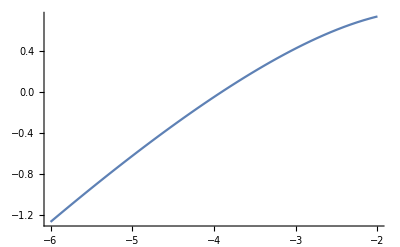

```mathematica
Plot[g[zc],{zc,-6,-2}]
```

Find the root near z=-4 and convert to ϵ_c

```mathematica
zcRoot=FindRoot[g[zc],{zc,-4}]
ϵcValue=ϵc/.ϵcFromzcRule/.zcRoot
```

NIntegrate::nlim: z = zc is not a valid limit of integration.

{zc→-3.90526}

0.215987

Even though Mma does arbitrary precision, it doesn’t perform that well here. But that’s ok, we have the python implementation using mpmath that works great.

### Bonus: interactive graphs

Here are the 0th order composite solutions:

```mathematica
Manipulate[Plot[Evaluate[{yc0B0[x],yc0M[x],yc0B1[x]}/.ϵ->eps],{x,0,1},PlotRange->{-2,2}],{{eps,.05},.006,.21}]
```

And here are the first order composite solutions:

```mathematica
Manipulate[Plot[Evaluate[{yc1B0[x],yc1M[x],yc1B1[x]}/.ϵ->eps],{x,0,1},PlotRange->{-2,2}],{{eps,.05},.006,.21}]
```

This is what the flow lines in phase space looks like

```mathematica
phaseSpaceVecField={y'[x],z'[x]}/.yPrimeRule/.zPrimeRule/.{y[x]->y,z[x]->z}//Simplify
```

{z,(y (-1+z))/ϵ}

```mathematica
Manipulate[
StreamPlot[{z,1/ϵ y(z-1)},{y,-2,2},{z,-4,1.5},
FrameLabel->{"y","y'"},
Epilog->{VertLine[1],VertLine[-1]}],
{{ϵ,.2},.001,.5}]
```